# Phase Transition with Extra Scalar at 10^5 GeV

```mathematica
ClearAll["Global`*"]
```

## Running parameters

### SM Parameters

```mathematica
sw = √0.23116;
cw = √(1 - sw^2);
mZ = 91.1876; 
mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)
GF = 1.16637 10^-5;
v=1/(√(√2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;(*Planck mass*)
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
```

### Running equations

```mathematica
(*Phase space factor*)
κ=1/(16*Pi^2); 

(*numbers of flavors*)
nf=6;
ng=3;
z3=Zeta[3];

(*QCD colour factors*)
ca=3;
dR=3;
cf=4/3;
cr=1/2;

(*Beta function for top-Yukawa*)βyt[λ_,yt_,g3_,g2_,g1_]:=2*yt*(+κ*yt^2*(3/4+1/2*dR)+κ*g3^2*(-3*cf)+κ^2*λ^2*(3)+κ^2*yt^2*λ*(-6)+κ^2*yt^4*(3/4-9/4*dR)+κ^2*g3^2*yt^2*(6*cf+5/2*cf*dR)+κ^2*g3^4*(-3/2*cf^2-97/6*ca*cf+10/3*nf*cr*cf)+κ^3*λ^3*(-18)+κ^3*yt^2*λ^2*(285/8-45/4*dR)+κ^3*yt^4*λ*(63/2+45/2*dR)+κ^3*yt^6*(-345/32+107/32*dR+39/16*dR^2+9/4*z3+3/2*z3*dR)+κ^3*g3^2*yt^2*λ*(6*cf)+κ^3*g3^2*yt^4*(-57/2*cf-81/8*cf*dR)+κ^3*g3^4*yt^2*(471/16*cf^2-119/8*cf^2*dR+25*cr*cf+717/16*ca*cf+77/4*ca*cf*dR-33/4*nf*cr*cf-4*nf*cr*cf*dR-27*z3*cf^2+18*z3*cf^2*dR-27/2*z3*ca*cf-9*z3*ca*cf*dR)+κ^3*g3^6*(-129/2*cf^3+129/4*ca*cf^2-11413/108*ca^2*cf+46*nf*cr*cf^2+556/27*nf*ca*cr*cf+140/27*nf^2*cr^2*cf-48*z3*nf*cr*cf^2+48*z3*nf*ca*cr*cf))+yt κ(-9/4 g2^2-17/12 g1^2)+yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45*ng)-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-ng)g2^4+9 g2^2 g3^2);

(*Beta function for the gauge couplings*)
βg3[λ_,yt_,g3_,g2_,g1_]:=2*g3*(+κ*g3^2*(-11/6*ca+2/3*nf*cr)+κ^2*g3^2*yt^2*(-2*cr)+κ^2*g3^4*(-17/3*ca^2+2*nf*cr*cf+10/3*nf*ca*cr)+κ^3*g3^2*yt^4*(9/2*cr+7/2*cr*dR)+κ^3*g3^4*yt^2*(-3*cr*cf-12*ca*cr)+κ^3*g3^6*(-2857/108*ca^3-nf*cr*cf^2+205/18*nf*ca*cr*cf+1415/54*nf*ca^2*cr-22/9*nf^2*cr^2*cf-79/27*nf^2*ca*cr^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_]:=-g1^3 κ(-1/6-20/9*ng)+g1^3 κ^2 5/3(199/30 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_]:=-g2^3 κ(43/6-4/3*ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);

(*Beta function for the quartic self-coupling of the scalar field*)
βλ[λ_,yt_,g3_,g2_,g1_]:=2*(+κ*λ^2*(12)+κ*yt^2*λ*(2*dR)+κ*yt^4*(-dR)+κ^2*λ^3*(-156)+κ^2*yt^2*λ^2*(-24*dR)+κ^2*yt^4*λ*(-1/2*dR)+κ^2*yt^6*(5*dR)+κ^2*g3^2*yt^2*λ*(10*cf*dR)+κ^2*g3^2*yt^4*(-4*cf*dR)+κ^3*λ^4*(3588+2016*z3)+κ^3*yt^2*λ^3*(291*dR)+κ^3*yt^4*λ^2*(789/2*dR-36*dR^2+252*z3*dR)+κ^3*yt^6*λ*(-1881/8*dR+80*dR^2-66*z3*dR)+κ^3*yt^8*(13/2*dR-195/8*dR^2-12*z3*dR)+κ^3*g3^2*yt^2*λ^2*(-306*cf*dR+288*z3*cf*dR)+κ^3*g3^2*yt^4*λ*(895/4*cf*dR-324*z3*cf*dR)+κ^3*g3^2*yt^6*(-19/2*cf*dR+60*z3*cf*dR)+κ^3*g3^4*yt^2*λ*(-119/2*cf^2*dR+77*ca*cf*dR-16*nf*cr*cf*dR+72*z3*cf^2*dR-36*z3*ca*cf*dR)+κ^3*g3^4*yt^4*(131/2*cf^2*dR+48*cr*cf*dR-109/2*ca*cf*dR+10*nf*cr*cf*dR-48*z3*cf^2*dR+24*z3*ca*cf*dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10ng)g2^4-39/4 g2^2 g1^2-(687/200+2ng)25/9 g1^4)2λ+(497/8-8ng)g2^6-(97/40+8/5 ng)5/3 g2^4 g1^2-(717/200+8/5 ng)25/9 g2^2 g1^4-(531/1000+24/25 ng)125/27 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10*2 λ yt^2(17/12 g1^2+9/4 g2^2));
βA[λ_,yt_,g3_,g2_,g1_,A_]=2κ A(6 λ+3 yt^2+3 yb^2+yτ^2-9/4 g2^2-9/20 g1^2);
(*measured gauge coupling*)
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;
g3mZ=√(4π*αsmZ);
αsmZ=0.1179;

(*Measured pole masses*)
mhpole=125.10;
mtpole=172.76;

(*MSbar couplings*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);
ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);
g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;
(*IW: should these equations be updated? These equations come from the near criticality paper, but that paper cites a measured value different from the current value*)
```

## Parametrization at T=0

```mathematica
μS2[mS_,sinθ_]:=sinθ^2 mhpole^2+(1-sinθ^2)mS^2;
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/v;
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
```

## Find Phase transition strength

```mathematica
vR=10^5;
aB=Exp[3.91];
aF=Exp[1.14];
```

```mathematica
transition‵strength[mS_,sinθ_]:=(
λbound=λhL[mS,sinθ];
Abound=A[mS,sinθ];
μS=√μS2[mS,sinθ];
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hA'[t]==βA[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],hA[t]],hA[Log[mtpole/mZ]]==Abound,hλ[Log[mtpole/mZ]]==λbound,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt,hA},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]},{Afun[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s,hA[Log[μ/mZ]]/.s};
g=g2[vR];
gY=g1[vR];
Avalue=Afun[vR];
λR=λ[vR];
ytR=yt[vR];
mWR=1/4 g^2 vR^2;
mZR=1/4(g^2+gY^2)vR^2;
mtR=1/2 ytR^2 vR^2;
DD=1/16(3 g^2+gY^2+4 ytR^2);
BB=3/(64 π^2 vR^4)(2 mWR^2+mZR^2-4 mtR^2);
EE=1/(32π)(2 g^3+(g^2+gY^2)^(3/2));
cs=1/3;
μH2=λR vR^2;
Deff=DD-(cs Avalue^2)/(4 μS^2);
λeff=λR-Avalue^2/(2 μS^2);
T0=√(1/(2Deff)(μH2-4 BB vR^2));
mgauge=({{g^2 x1^2/4+11/6 g^2 x2^2, -g gY x1^2/4}, {-g gY x1^2/4, gY^2 x1^2/4+11/3 gY^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g^2 ϕ^2+11/6 gY^2 T^2;(*longitudal mode for W+ and W-, or W1 and W2*)
mBL[ϕ_,T_]:=gaugeL[[1]]/.{x1->ϕ,x2->T};(*SM B particle, massless*)
mZL[ϕ_,T_]:=gaugeL[[2]]/.{x1->ϕ,x2->T};(*Zprime particle*)
λT[T_]:=λeff-3/(16 π^2 vR^4)(2 mWR^2 Log[mWR/(aB T^2)]+mZR^2 Log[mZR/(aB T^2)]-4 mtR^2 Log[mtR/(aF T^2)]);
resum[ϕ_,T_]:=T/(12π)(2((mWR ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZR ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
VhighT[ϕ_,T_]:=Deff(T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[VhighT[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc
)
```

```mathematica
transition‵strength[5,0.023]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

1.15323

```mathematica
list=Table[{mS,sinθ,transition‵strength[mS,sinθ]},{mS,0.1,10,1},{sinθ,0.0001,0.05,0.001}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::nrnum: The function value 1.8903×10^9 (-1.5121×10^9+(-3888.57+Null)^2)-8.37376×10^12 (-3888.57+Null)-((-«18»+«4»)«1»«1»)/(12 π)+((-3888.57+«4») «1»)/(12 π)+2.5×10^19 (-0.0550283-(3 (1.80642×10^18 Log[Times[«2»]]+1.67843×10^18 Log[«1»]-2.58527×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

FindMinimum::nrnum: The function value 1.8903×10^9 (-1.5121×10^9+(-3499.71+Null)^2)-8.37376×10^12 (-3499.71+Null)-((«1») «1»)/(12 π)+((-3499.71+«4»)«1»«1»)/(12 π)+2.5×10^19 (-0.0550283-(3 (1.80642×10^18 Log[Times[«2»]]+1.67843×10^18 Log[«1»]-2.58527×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

FindMinimum::nrnum: The function value 1.8903×10^9 (-1.5121×10^9+(-3110.86+Null)^2)-8.37376×10^12 (-3110.86+Null)-((«1») «1»)/(12 π)+((-3110.86+«4»)«1»«1»)/(12 π)+2.5×10^19 (-0.0550283-(3 (1.80642×10^18 Log[Times[«2»]]+1.67843×10^18 Log[«1»]-2.58527×10^19 Log[Times[«2»]]))/(1600000000000000000000 π^2)) is not a real number at {ϕ} = {100000.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,100000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

{{{0.1,0.0001,0.231418},{0.1,0.0011,(ϕ/.{ϕ,100000})/Null},{0.1,0.0021,(ϕ/.{ϕ,100000})/Null},{0.1,0.0031,(ϕ/.{ϕ,100000})/Null},{0.1,0.0041,(ϕ/.{ϕ,100000})/Null},{0.1,0.0051,(ϕ/.{ϕ,100000})/Null},{0.1,0.0061,(ϕ/.{ϕ,100000})/Null},{0.1,0.0071,(ϕ/.{ϕ,100000})/Null},{0.1,0.0081,(ϕ/.{ϕ,100000})/Null},{0.1,0.0091,(ϕ/.{ϕ,100000})/Null},{0.1,0.0101,(ϕ/.{ϕ,100000})/Null},{0.1,0.0111,(ϕ/.{ϕ,100000})/Null},{0.1,0.0121,(ϕ/.{ϕ,100000})/Null},{0.1,0.0131,(ϕ/.{ϕ,100000})/Null},{0.1,0.0141,(ϕ/.{ϕ,100000})/Null},{0.1,0.0151,(ϕ/.{ϕ,100000})/Null},{0.1,0.0161,(ϕ/.{ϕ,100000})/Null},{0.1,0.0171,(ϕ/.{ϕ,100000})/Null},{0.1,0.0181,(ϕ/.{ϕ,100000})/Null},{0.1,0.0191,(ϕ/.{ϕ,100000})/Null},{0.1,0.0201,(ϕ/.{ϕ,100000})/Null},{0.1,0.0211,(ϕ/.{ϕ,100000})/Null},{0.1,0.0221,(ϕ/.{ϕ,100000})/Null},{0.1,0.0231,(ϕ/.{ϕ,100000})/Null},{0.1,0.0241,(ϕ/.{ϕ,100000})/Null},{0.1,0.0251,(ϕ/.{ϕ,100000})/Null},{0.1,0.0261,(ϕ/.{ϕ,100000})/Null},{0.1,0.0271,(ϕ/.{ϕ,100000})/Null},{0.1,0.0281,(ϕ/.{ϕ,100000})/Null},{0.1,0.0291,(ϕ/.{ϕ,100000})/Null},{0.1,0.0301,(ϕ/.{ϕ,100000})/Null},{0.1,0.0311,(ϕ/.{ϕ,100000})/Null},{0.1,0.0321,(ϕ/.{ϕ,100000})/Null},{0.1,0.0331,(ϕ/.{ϕ,100000})/Null},{0.1,0.0341,(ϕ/.{ϕ,100000})/Null},{0.1,0.0351,(ϕ/.{ϕ,100000})/Null},{0.1,0.0361,(ϕ/.{ϕ,100000})/Null},{0.1,0.0371,(ϕ/.{ϕ,100000})/Null},{0.1,0.0381,(ϕ/.{ϕ,100000})/Null},{0.1,0.0391,(ϕ/.{ϕ,100000})/Null},{0.1,0.0401,(ϕ/.{ϕ,100000})/Null},{0.1,0.0411,(ϕ/.{ϕ,100000})/Null},{0.1,0.0421,(ϕ/.{ϕ,100000})/Null},{0.1,0.0431,(ϕ/.{ϕ,100000})/Null},{0.1,0.0441,(ϕ/.{ϕ,100000})/Null},{0.1,0.0451,(ϕ/.{ϕ,100000})/Null},{0.1,0.0461,(ϕ/.{ϕ,100000})/Null},{0.1,0.0471,(ϕ/.{ϕ,100000})/Null},{0.1,0.0481,(ϕ/.{ϕ,100000})/Null},{0.1,0.0491,(ϕ/.{ϕ,100000})/Null}},{{1.1,0.0001,0.22004},{1.1,0.0011,0.231414},{1.1,0.0021,0.267201},{1.1,0.0031,0.344679},{1.1,0.0041,0.529095},{1.1,0.0051,1.21961},{1.1,0.0061,1.12291×10^-6},{1.1,0.0071,(ϕ/.{ϕ,100000})/Null},{1.1,0.0081,(ϕ/.{ϕ,100000})/Null},{1.1,0.0091,(ϕ/.{ϕ,100000})/Null},{1.1,0.0101,(ϕ/.{ϕ,100000})/Null},{1.1,0.0111,(ϕ/.{ϕ,100000})/Null},{1.1,0.0121,(ϕ/.{ϕ,100000})/Null},{1.1,0.0131,(ϕ/.{ϕ,100000})/Null},{1.1,0.0141,(ϕ/.{ϕ,100000})/Null},{1.1,0.0151,(ϕ/.{ϕ,100000})/Null},{1.1,0.0161,(ϕ/.{ϕ,100000})/Null},{1.1,0.0171,(ϕ/.{ϕ,100000})/Null},{1.1,0.0181,(ϕ/.{ϕ,100000})/Null},{1.1,0.0191,(ϕ/.{ϕ,100000})/Null},{1.1,0.0201,(ϕ/.{ϕ,100000})/Null},{1.1,0.0211,(ϕ/.{ϕ,100000})/Null},{1.1,0.0221,(ϕ/.{ϕ,100000})/Null},{1.1,0.0231,(ϕ/.{ϕ,100000})/Null},{1.1,0.0241,(ϕ/.{ϕ,100000})/Null},{1.1,0.0251,(ϕ/.{ϕ,100000})/Null},{1.1,0.0261,(ϕ/.{ϕ,100000})/Null},{1.1,0.0271,(ϕ/.{ϕ,100000})/Null},{1.1,0.0281,(ϕ/.{ϕ,100000})/Null},{1.1,0.0291,(ϕ/.{ϕ,100000})/Null},{1.1,0.0301,(ϕ/.{ϕ,100000})/Null},{1.1,0.0311,(ϕ/.{ϕ,100000})/Null},{1.1,0.0321,(ϕ/.{ϕ,100000})/Null},{1.1,0.0331,(ϕ/.{ϕ,100000})/Null},{1.1,0.0341,(ϕ/.{ϕ,100000})/Null},{1.1,0.0351,(ϕ/.{ϕ,100000})/Null},{1.1,0.0361,(ϕ/.{ϕ,100000})/Null},{1.1,0.0371,(ϕ/.{ϕ,100000})/Null},{1.1,0.0381,(ϕ/.{ϕ,100000})/Null},{1.1,0.0391,(ϕ/.{ϕ,100000})/Null},{1.1,0.0401,(ϕ/.{ϕ,100000})/Null},{1.1,0.0411,(ϕ/.{ϕ,100000})/Null},{1.1,0.0421,(ϕ/.{ϕ,100000})/Null},{1.1,0.0431,(ϕ/.{ϕ,100000})/Null},{1.1,0.0441,(ϕ/.{ϕ,100000})/Null},{1.1,0.0451,(ϕ/.{ϕ,100000})/Null},{1.1,0.0461,(ϕ/.{ϕ,100000})/Null},{1.1,0.0471,(ϕ/.{ϕ,100000})/Null},{1.1,0.0481,(ϕ/.{ϕ,100000})/Null},{1.1,0.0491,(ϕ/.{ϕ,100000})/Null}},{{2.1,0.0001,0.219865},{2.1,0.0011,0.223622},{2.1,0.0021,0.231407},{2.1,0.0031,0.246338},{2.1,0.0041,0.269005},{2.1,0.0051,0.304297},{2.1,0.0061,0.355776},{2.1,0.0071,0.436714},{2.1,0.0081,0.574983},{2.1,0.0091,0.850282},{2.1,0.0101,1.6057},{2.1,0.0111,-1.55976×10^-6},{2.1,0.0121,0.000036502},{2.1,0.0131,3.43342×10^-7},{2.1,0.0141,(ϕ/.{ϕ,100000})/Null},{2.1,0.0151,(ϕ/.{ϕ,100000})/Null},{2.1,0.0161,(ϕ/.{ϕ,100000})/Null},{2.1,0.0171,(ϕ/.{ϕ,100000})/Null},{2.1,0.0181,(ϕ/.{ϕ,100000})/Null},{2.1,0.0191,(ϕ/.{ϕ,100000})/Null},{2.1,0.0201,(ϕ/.{ϕ,100000})/Null},{2.1,0.0211,(ϕ/.{ϕ,100000})/Null},{2.1,0.0221,(ϕ/.{ϕ,100000})/Null},{2.1,0.0231,(ϕ/.{ϕ,100000})/Null},{2.1,0.0241,(ϕ/.{ϕ,100000})/Null},{2.1,0.0251,(ϕ/.{ϕ,100000})/Null},{2.1,0.0261,(ϕ/.{ϕ,100000})/Null},{2.1,0.0271,(ϕ/.{ϕ,100000})/Null},{2.1,0.0281,(ϕ/.{ϕ,100000})/Null},{2.1,0.0291,(ϕ/.{ϕ,100000})/Null},{2.1,0.0301,(ϕ/.{ϕ,100000})/Null},{2.1,0.0311,(ϕ/.{ϕ,100000})/Null},{2.1,0.0321,(ϕ/.{ϕ,100000})/Null},{2.1,0.0331,(ϕ/.{ϕ,100000})/Null},{2.1,0.0341,(ϕ/.{ϕ,100000})/Null},{2.1,0.0351,(ϕ/.{ϕ,100000})/Null},{2.1,0.0361,(ϕ/.{ϕ,100000})/Null},{2.1,0.0371,(ϕ/.{ϕ,100000})/Null},{2.1,0.0381,(ϕ/.{ϕ,100000})/Null},{2.1,0.0391,(ϕ/.{ϕ,100000})/Null},{2.1,0.0401,(ϕ/.{ϕ,100000})/Null},{2.1,0.0411,(ϕ/.{ϕ,100000})/Null},{2.1,0.0421,(ϕ/.{ϕ,100000})/Null},{2.1,0.0431,(ϕ/.{ϕ,100000})/Null},{2.1,0.0441,(ϕ/.{ϕ,100000})/Null},{2.1,0.0451,(ϕ/.{ϕ,100000})/Null},{2.1,0.0461,(ϕ/.{ϕ,100000})/Null},{2.1,0.0471,(ϕ/.{ϕ,100000})/Null},{2.1,0.0481,(ϕ/.{ϕ,100000})/Null},{2.1,0.0491,(ϕ/.{ϕ,100000})/Null}},{{3.1,0.0001,0.219829},{3.1,0.0011,0.220658},{3.1,0.0021,0.224875},{3.1,0.0031,0.231395},{3.1,0.0041,0.240811},{3.1,0.0051,0.254051},{3.1,0.0061,0.271132},{3.1,0.0071,0.292807},{3.1,0.0081,0.320966},{3.1,0.0091,0.359412},{3.1,0.0101,0.411183},{3.1,0.0111,0.484453},{3.1,0.0121,0.592986},{3.1,0.0131,0.766546},{3.1,0.0141,1.08128},{3.1,0.0151,1.80162},{3.1,0.0161,4.65926},{3.1,0.0171,-6.16591×10^-6},{3.1,0.0181,1.44232×10^-6},{3.1,0.0191,1.36567×10^-6},{3.1,0.0201,(ϕ/.{ϕ,100000})/Null},{3.1,0.0211,(ϕ/.{ϕ,100000})/Null},{3.1,0.0221,(ϕ/.{ϕ,100000})/Null},{3.1,0.0231,(ϕ/.{ϕ,100000})/Null},{3.1,0.0241,(ϕ/.{ϕ,100000})/Null},{3.1,0.0251,(ϕ/.{ϕ,100000})/Null},{3.1,0.0261,(ϕ/.{ϕ,100000})/Null},{3.1,0.0271,(ϕ/.{ϕ,100000})/Null},{3.1,0.0281,(ϕ/.{ϕ,100000})/Null},{3.1,0.0291,(ϕ/.{ϕ,100000})/Null},{3.1,0.0301,(ϕ/.{ϕ,100000})/Null},{3.1,0.0311,(ϕ/.{ϕ,100000})/Null},{3.1,0.0321,(ϕ/.{ϕ,100000})/Null},{3.1,0.0331,(ϕ/.{ϕ,100000})/Null},{3.1,0.0341,(ϕ/.{ϕ,100000})/Null},{3.1,0.0351,(ϕ/.{ϕ,100000})/Null},{3.1,0.0361,(ϕ/.{ϕ,100000})/Null},{3.1,0.0371,(ϕ/.{ϕ,100000})/Null},{3.1,0.0381,(ϕ/.{ϕ,100000})/Null},{3.1,0.0391,(ϕ/.{ϕ,100000})/Null},{3.1,0.0401,(ϕ/.{ϕ,100000})/Null},{3.1,0.0411,(ϕ/.{ϕ,100000})/Null},{3.1,0.0421,(ϕ/.{ϕ,100000})/Null},{3.1,0.0431,(ϕ/.{ϕ,100000})/Null},{3.1,0.0441,(ϕ/.{ϕ,100000})/Null},{3.1,0.0451,(ϕ/.{ϕ,100000})/Null},{3.1,0.0461,(ϕ/.{ϕ,100000})/Null},{3.1,0.0471,(ϕ/.{ϕ,100000})/Null},{3.1,0.0481,(ϕ/.{ϕ,100000})/Null},{3.1,0.0491,(ϕ/.{ϕ,100000})/Null}},{{4.1,0.0001,0.219816},{4.1,0.0011,0.22049},{4.1,0.0021,0.223261},{4.1,0.0031,0.22683},{4.1,0.0041,0.231378},{4.1,0.0051,0.238575},{4.1,0.0061,0.247395},{4.1,0.0071,0.25836},{4.1,0.0081,0.270793},{4.1,0.0091,0.287051},{4.1,0.0101,0.307085},{4.1,0.0111,0.33139},{4.1,0.0121,0.361281},{4.1,0.0131,0.400716},{4.1,0.0141,0.448916},{4.1,0.0151,0.514201},{4.1,0.0161,0.602173},{4.1,0.0171,0.729505},{4.1,0.0181,0.922963},{4.1,0.0191,1.25389},{4.1,0.0201,1.91766},{4.1,0.0211,3.78319},{4.1,0.0221,-4.21818×10^-6},{4.1,0.0231,-9.49236×10^-7},{4.1,0.0241,1.50093×10^-6},{4.1,0.0251,7.50451×10^-7},{4.1,0.0261,(ϕ/.{ϕ,100000})/Null},{4.1,0.0271,(ϕ/.{ϕ,100000})/Null},{4.1,0.0281,(ϕ/.{ϕ,100000})/Null},{4.1,0.0291,(ϕ/.{ϕ,100000})/Null},{4.1,0.0301,(ϕ/.{ϕ,100000})/Null},{4.1,0.0311,(ϕ/.{ϕ,100000})/Null},{4.1,0.0321,(ϕ/.{ϕ,100000})/Null},{4.1,0.0331,(ϕ/.{ϕ,100000})/Null},{4.1,0.0341,(ϕ/.{ϕ,100000})/Null},{4.1,0.0351,(ϕ/.{ϕ,100000})/Null},{4.1,0.0361,(ϕ/.{ϕ,100000})/Null},{4.1,0.0371,(ϕ/.{ϕ,100000})/Null},{4.1,0.0381,(ϕ/.{ϕ,100000})/Null},{4.1,0.0391,(ϕ/.{ϕ,100000})/Null},{4.1,0.0401,(ϕ/.{ϕ,100000})/Null},{4.1,0.0411,(ϕ/.{ϕ,100000})/Null},{4.1,0.0421,(ϕ/.{ϕ,100000})/Null},{4.1,0.0431,(ϕ/.{ϕ,100000})/Null},{4.1,0.0441,(ϕ/.{ϕ,100000})/Null},{4.1,0.0451,(ϕ/.{ϕ,100000})/Null},{4.1,0.0461,(ϕ/.{ϕ,100000})/Null},{4.1,0.0471,(ϕ/.{ϕ,100000})/Null},{4.1,0.0481,(ϕ/.{ϕ,100000})/Null},{4.1,0.0491,(ϕ/.{ϕ,100000})/Null}},{{5.1,0.0001,0.21981},{5.1,0.0011,0.219742},{5.1,0.0021,0.221935},{5.1,0.0031,0.223606},{5.1,0.0041,0.227651},{5.1,0.0051,0.231356},{5.1,0.0061,0.236272},{5.1,0.0071,0.243991},{5.1,0.0081,0.25056},{5.1,0.0091,0.260487},{5.1,0.0101,0.271381},{5.1,0.0111,0.283768},{5.1,0.0121,0.299705},{5.1,0.0131,0.317305},{5.1,0.0141,0.33774},{5.1,0.0151,0.362578},{5.1,0.0161,0.393966},{5.1,0.0171,0.43082},{5.1,0.0181,0.476161},{5.1,0.0191,0.533816},{5.1,0.0201,0.608609},{5.1,0.0211,0.708029},{5.1,0.0221,0.847222},{5.1,0.0231,1.05343},{5.1,0.0241,1.38475},{5.1,0.0251,1.99082},{5.1,0.0261,3.38596},{5.1,0.0271,9.19594×10^-6},{5.1,0.0281,-2.12075×10^-6},{5.1,0.0291,4.95988×10^-6},{5.1,0.0301,2.72812×10^-6},{5.1,0.0311,2.39439×10^-6},{5.1,0.0321,8.41837×10^-7},{5.1,0.0331,(ϕ/.{ϕ,100000})/Null},{5.1,0.0341,(ϕ/.{ϕ,100000})/Null},{5.1,0.0351,(ϕ/.{ϕ,100000})/Null},{5.1,0.0361,(ϕ/.{ϕ,100000})/Null},{5.1,0.0371,(ϕ/.{ϕ,100000})/Null},{5.1,0.0381,(ϕ/.{ϕ,100000})/Null},{5.1,0.0391,(ϕ/.{ϕ,100000})/Null},{5.1,0.0401,(ϕ/.{ϕ,100000})/Null},{5.1,0.0411,(ϕ/.{ϕ,100000})/Null},{5.1,0.0421,(ϕ/.{ϕ,100000})/Null},{5.1,0.0431,(ϕ/.{ϕ,100000})/Null},{5.1,0.0441,(ϕ/.{ϕ,100000})/Null},{5.1,0.0451,(ϕ/.{ϕ,100000})/Null},{5.1,0.0461,(ϕ/.{ϕ,100000})/Null},{5.1,0.0471,(ϕ/.{ϕ,100000})/Null},{5.1,0.0481,(ϕ/.{ϕ,100000})/Null},{5.1,0.0491,(ϕ/.{ϕ,100000})/Null}},{{6.1,0.0001,0.219806},{6.1,0.0011,0.220743},{6.1,0.0021,0.221844},{6.1,0.0031,0.22313},{6.1,0.0041,0.224632},{6.1,0.0051,0.227813},{6.1,0.0061,0.23133},{6.1,0.0071,0.235265},{6.1,0.0081,0.241139},{6.1,0.0091,0.247671},{6.1,0.0101,0.253639},{6.1,0.0111,0.26204},{6.1,0.0121,0.271723},{6.1,0.0131,0.281613},{6.1,0.0141,0.293483},{6.1,0.0151,0.307818},{6.1,0.0161,0.323832},{6.1,0.0171,6.27482×10^-7},{6.1,0.0181,0.364211},{6.1,0.0191,0.389488},{6.1,0.0201,0.418494},{6.1,0.0211,0.453554},{6.1,0.0221,0.495187},{6.1,0.0231,0.546646},{6.1,0.0241,0.612001},{6.1,0.0251,0.693598},{6.1,0.0261,0.801465},{6.1,0.0271,0.949519},{6.1,0.0281,1.16024},{6.1,0.0291,1.48666},{6.1,0.0301,2.03928},{6.1,0.0311,3.15298},{6.1,0.0321,2.88531×10^-6},{6.1,0.0331,-4.69192×10^-6},{6.1,0.0341,-4.28064×10^-8},{6.1,0.0351,-4.98593×10^-6},{6.1,0.0361,8.42847×10^-7},{6.1,0.0371,-3.26669×10^-6},{6.1,0.0381,-1.19508×10^-7},{6.1,0.0391,(ϕ/.{ϕ,100000})/Null},{6.1,0.0401,(ϕ/.{ϕ,100000})/Null},{6.1,0.0411,(ϕ/.{ϕ,100000})/Null},{6.1,0.0421,(ϕ/.{ϕ,100000})/Null},{6.1,0.0431,(ϕ/.{ϕ,100000})/Null},{6.1,0.0441,(ϕ/.{ϕ,100000})/Null},{6.1,0.0451,(ϕ/.{ϕ,100000})/Null},{6.1,0.0461,(ϕ/.{ϕ,100000})/Null},{6.1,0.0471,(ϕ/.{ϕ,100000})/Null},{6.1,0.0481,(ϕ/.{ϕ,100000})/Null},{6.1,0.0491,(ϕ/.{ϕ,100000})/Null}},{{7.1,0.0001,0.219805},{7.1,0.0011,0.220495},{7.1,0.0021,0.220937},{7.1,0.0031,0.222542},{7.1,0.0041,0.22393},{7.1,0.0051,0.225121},{7.1,0.0061,0.228968},{7.1,0.0071,0.231298},{7.1,0.0081,0.234972},{7.1,0.0091,0.240056},{7.1,0.0101,0.243833},{7.1,0.0111,0.250597},{7.1,0.0121,0.256272},{7.1,0.0131,0.263786},{7.1,0.0141,0.271912},{7.1,0.0151,0.280851},{7.1,0.0161,0.290844},{7.1,0.0171,0.302181},{7.1,0.0181,0.315214},{7.1,0.0191,0.328997},{7.1,0.0201,0.345443},{7.1,0.0211,0.363839},{7.1,0.0221,0.385028},{7.1,0.0231,0.410078},{7.1,0.0241,0.439002},{7.1,0.0251,0.472266},{7.1,0.0261,0.510967},{7.1,0.0271,0.557101},{7.1,0.0281,0.614028},{7.1,0.0291,0.68322},{7.1,0.0301,0.772247},{7.1,0.0311,0.885311},{7.1,0.0321,1.03723},{7.1,0.0331,1.25038},{7.1,0.0341,1.56578},{7.1,0.0351,2.07084},{7.1,0.0361,2.99627},{7.1,0.0371,-1.90911×10^-6},{7.1,0.0381,-0.0000126526},{7.1,0.0391,4.85272×10^-7},{7.1,0.0401,-3.07225×10^-6},{7.1,0.0411,2.7639×10^-6},{7.1,0.0421,3.6787×10^-6},{7.1,0.0431,-3.38532×10^-7},{7.1,0.0441,1.18981×10^-6},{7.1,0.0451,(ϕ/.{ϕ,100000})/Null},{7.1,0.0461,(ϕ/.{ϕ,100000})/Null},{7.1,0.0471,(ϕ/.{ϕ,100000})/Null},{7.1,0.0481,(ϕ/.{ϕ,100000})/Null},{7.1,0.0491,(ϕ/.{ϕ,100000})/Null}},{{8.1,0.0001,0.219803},{8.1,0.0011,0.220332},{8.1,0.0021,0.220342},{8.1,0.0031,0.221245},{8.1,0.0041,0.223052},{8.1,0.0051,0.224372},{8.1,0.0061,0.22663},{8.1,0.0071,0.228448},{8.1,0.0081,0.231262},{8.1,0.0091,0.235107},{8.1,0.0101,0.238627},{8.1,0.0111,0.241872},{8.1,0.0121,0.247709},{8.1,0.0131,0.252012},{8.1,0.0141,0.257658},{8.1,0.0151,0.264747},{8.1,0.0161,0.271997},{8.1,0.0171,0.27955},{8.1,0.0181,0.287563},{8.1,0.0191,0.297617},{8.1,0.0201,0.30854},{8.1,0.0211,0.320602},{8.1,0.0221,0.332745},{8.1,0.0231,0.348113},{8.1,0.0241,0.364412},{8.1,0.0251,0.383593},{8.1,0.0261,0.403629},{8.1,0.0271,0.428139},{8.1,0.0281,0.455518},{8.1,0.0291,0.485863},{8.1,0.0301,0.52241},{8.1,0.0311,0.56496},{8.1,0.0321,0.615563},{8.1,0.0331,0.676259},{8.1,0.0341,0.749794},{8.1,0.0351,0.842123},{8.1,0.0361,0.959294},{8.1,0.0371,1.11407},{8.1,0.0381,1.32625},{8.1,0.0391,1.62832},{8.1,0.0401,2.09158},{8.1,0.0411,2.87893},{8.1,0.0421,4.52705},{8.1,0.0431,-0.0000148476},{8.1,0.0441,4.99223×10^-6},{8.1,0.0451,3.07616×10^-6},{8.1,0.0461,(ϕ/.{ϕ,100000})/Null},{8.1,0.0471,-3.23242×10^-6},{8.1,0.0481,7.40772×10^-8},{8.1,0.0491,-4.28622×10^-8}},{{9.1,0.0001,0.219803},{9.1,0.0011,0.220222},{9.1,0.0021,0.219932},{9.1,0.0031,0.221758},{9.1,0.0041,0.221481},{9.1,0.0051,0.223336},{9.1,0.0061,0.224511},{9.1,0.0071,0.226442},{9.1,0.0081,0.22914},{9.1,0.0091,0.231221},{9.1,0.0101,0.234121},{9.1,0.0111,0.237866},{9.1,0.0121,0.241094},{9.1,0.0131,0.245244},{9.1,0.0141,0.248969},{9.1,0.0151,0.253717},{9.1,0.0161,0.259557},{9.1,0.0171,0.265161},{9.1,0.0181,0.272005},{9.1,0.0191,0.278799},{9.1,0.0201,0.285652},{9.1,0.0211,0.294084},{9.1,0.0221,0.302854},{9.1,0.0231,0.313525},{9.1,0.0241,0.324913},{9.1,0.0251,0.337261},{9.1,0.0261,0.349486},{9.1,0.0271,0.364675},{9.1,0.0281,0.380487},{9.1,0.0291,0.398791},{9.1,0.0301,0.420184},{9.1,0.0311,0.442679},{9.1,0.0321,0.468563},{9.1,0.0331,0.497639},{9.1,0.0341,0.531388},{9.1,0.0351,0.570374},{9.1,0.0361,0.615778},{9.1,0.0371,0.669642},{9.1,0.0381,0.733944},{9.1,0.0391,0.809955},{9.1,0.0401,0.905821},{9.1,0.0411,1.02535},{9.1,0.0421,1.1805},{9.1,0.0431,1.38884},{9.1,0.0441,1.67754},{9.1,0.0451,2.10396},{9.1,0.0461,2.78597},{9.1,0.0471,4.06055},{9.1,0.0481,7.75433×10^-6},{9.1,0.0491,1.86079×10^-6}}}

```mathematica
list1=Flatten[list,1]
```

{{0.1,0.0001,0.231418},{0.1,0.0011,(ϕ/.{ϕ,100000})/Null},{0.1,0.0021,(ϕ/.{ϕ,100000})/Null},{0.1,0.0031,(ϕ/.{ϕ,100000})/Null},{0.1,0.0041,(ϕ/.{ϕ,100000})/Null},{0.1,0.0051,(ϕ/.{ϕ,100000})/Null},{0.1,0.0061,(ϕ/.{ϕ,100000})/Null},{0.1,0.0071,(ϕ/.{ϕ,100000})/Null},{0.1,0.0081,(ϕ/.{ϕ,100000})/Null},{0.1,0.0091,(ϕ/.{ϕ,100000})/Null},{0.1,0.0101,(ϕ/.{ϕ,100000})/Null},{0.1,0.0111,(ϕ/.{ϕ,100000})/Null},{0.1,0.0121,(ϕ/.{ϕ,100000})/Null},{0.1,0.0131,(ϕ/.{ϕ,100000})/Null},{0.1,0.0141,(ϕ/.{ϕ,100000})/Null},{0.1,0.0151,(ϕ/.{ϕ,100000})/Null},{0.1,0.0161,(ϕ/.{ϕ,100000})/Null},{0.1,0.0171,(ϕ/.{ϕ,100000})/Null},{0.1,0.0181,(ϕ/.{ϕ,100000})/Null},{0.1,0.0191,(ϕ/.{ϕ,100000})/Null},{0.1,0.0201,(ϕ/.{ϕ,100000})/Null},{0.1,0.0211,(ϕ/.{ϕ,100000})/Null},{0.1,0.0221,(ϕ/.{ϕ,100000})/Null},{0.1,0.0231,(ϕ/.{ϕ,100000})/Null},{0.1,0.0241,(ϕ/.{ϕ,100000})/Null},{0.1,0.0251,(ϕ/.{ϕ,100000})/Null},{0.1,0.0261,(ϕ/.{ϕ,100000})/Null},{0.1,0.0271,(ϕ/.{ϕ,100000})/Null},{0.1,0.0281,(ϕ/.{ϕ,100000})/Null},{0.1,0.0291,(ϕ/.{ϕ,100000})/Null},{0.1,0.0301,(ϕ/.{ϕ,100000})/Null},{0.1,0.0311,(ϕ/.{ϕ,100000})/Null},{0.1,0.0321,(ϕ/.{ϕ,100000})/Null},{0.1,0.0331,(ϕ/.{ϕ,100000})/Null},{0.1,0.0341,(ϕ/.{ϕ,100000})/Null},{0.1,0.0351,(ϕ/.{ϕ,100000})/Null},{0.1,0.0361,(ϕ/.{ϕ,100000})/Null},{0.1,0.0371,(ϕ/.{ϕ,100000})/Null},{0.1,0.0381,(ϕ/.{ϕ,100000})/Null},{0.1,0.0391,(ϕ/.{ϕ,100000})/Null},{0.1,0.0401,(ϕ/.{ϕ,100000})/Null},{0.1,0.0411,(ϕ/.{ϕ,100000})/Null},{0.1,0.0421,(ϕ/.{ϕ,100000})/Null},{0.1,0.0431,(ϕ/.{ϕ,100000})/Null},{0.1,0.0441,(ϕ/.{ϕ,100000})/Null},{0.1,0.0451,(ϕ/.{ϕ,100000})/Null},{0.1,0.0461,(ϕ/.{ϕ,100000})/Null},{0.1,0.0471,(ϕ/.{ϕ,100000})/Null},{0.1,0.0481,(ϕ/.{ϕ,100000})/Null},{0.1,0.0491,(ϕ/.{ϕ,100000})/Null},{1.1,0.0001,0.22004},{1.1,0.0011,0.231414},{1.1,0.0021,0.267201},{1.1,0.0031,0.344679},{1.1,0.0041,0.529095},{1.1,0.0051,1.21961},{1.1,0.0061,1.12291×10^-6},{1.1,0.0071,(ϕ/.{ϕ,100000})/Null},{1.1,0.0081,(ϕ/.{ϕ,100000})/Null},{1.1,0.0091,(ϕ/.{ϕ,100000})/Null},{1.1,0.0101,(ϕ/.{ϕ,100000})/Null},{1.1,0.0111,(ϕ/.{ϕ,100000})/Null},{1.1,0.0121,(ϕ/.{ϕ,100000})/Null},{1.1,0.0131,(ϕ/.{ϕ,100000})/Null},{1.1,0.0141,(ϕ/.{ϕ,100000})/Null},{1.1,0.0151,(ϕ/.{ϕ,100000})/Null},{1.1,0.0161,(ϕ/.{ϕ,100000})/Null},{1.1,0.0171,(ϕ/.{ϕ,100000})/Null},{1.1,0.0181,(ϕ/.{ϕ,100000})/Null},{1.1,0.0191,(ϕ/.{ϕ,100000})/Null},{1.1,0.0201,(ϕ/.{ϕ,100000})/Null},{1.1,0.0211,(ϕ/.{ϕ,100000})/Null},{1.1,0.0221,(ϕ/.{ϕ,100000})/Null},{1.1,0.0231,(ϕ/.{ϕ,100000})/Null},{1.1,0.0241,(ϕ/.{ϕ,100000})/Null},{1.1,0.0251,(ϕ/.{ϕ,100000})/Null},{1.1,0.0261,(ϕ/.{ϕ,100000})/Null},{1.1,0.0271,(ϕ/.{ϕ,100000})/Null},{1.1,0.0281,(ϕ/.{ϕ,100000})/Null},{1.1,0.0291,(ϕ/.{ϕ,100000})/Null},{1.1,0.0301,(ϕ/.{ϕ,100000})/Null},{1.1,0.0311,(ϕ/.{ϕ,100000})/Null},{1.1,0.0321,(ϕ/.{ϕ,100000})/Null},{1.1,0.0331,(ϕ/.{ϕ,100000})/Null},{1.1,0.0341,(ϕ/.{ϕ,100000})/Null},{1.1,0.0351,(ϕ/.{ϕ,100000})/Null},{1.1,0.0361,(ϕ/.{ϕ,100000})/Null},{1.1,0.0371,(ϕ/.{ϕ,100000})/Null},{1.1,0.0381,(ϕ/.{ϕ,100000})/Null},{1.1,0.0391,(ϕ/.{ϕ,100000})/Null},{1.1,0.0401,(ϕ/.{ϕ,100000})/Null},{1.1,0.0411,(ϕ/.{ϕ,100000})/Null},{1.1,0.0421,(ϕ/.{ϕ,100000})/Null},{1.1,0.0431,(ϕ/.{ϕ,100000})/Null},{1.1,0.0441,(ϕ/.{ϕ,100000})/Null},{1.1,0.0451,(ϕ/.{ϕ,100000})/Null},{1.1,0.0461,(ϕ/.{ϕ,100000})/Null},{1.1,0.0471,(ϕ/.{ϕ,100000})/Null},{1.1,0.0481,(ϕ/.{ϕ,100000})/Null},{1.1,0.0491,(ϕ/.{ϕ,100000})/Null},{2.1,0.0001,0.219865},{2.1,0.0011,0.223622},{2.1,0.0021,0.231407},{2.1,0.0031,0.246338},{2.1,0.0041,0.269005},{2.1,0.0051,0.304297},{2.1,0.0061,0.355776},{2.1,0.0071,0.436714},{2.1,0.0081,0.574983},{2.1,0.0091,0.850282},{2.1,0.0101,1.6057},{2.1,0.0111,-1.55976×10^-6},{2.1,0.0121,0.000036502},{2.1,0.0131,3.43342×10^-7},{2.1,0.0141,(ϕ/.{ϕ,100000})/Null},{2.1,0.0151,(ϕ/.{ϕ,100000})/Null},{2.1,0.0161,(ϕ/.{ϕ,100000})/Null},{2.1,0.0171,(ϕ/.{ϕ,100000})/Null},{2.1,0.0181,(ϕ/.{ϕ,100000})/Null},{2.1,0.0191,(ϕ/.{ϕ,100000})/Null},{2.1,0.0201,(ϕ/.{ϕ,100000})/Null},{2.1,0.0211,(ϕ/.{ϕ,100000})/Null},{2.1,0.0221,(ϕ/.{ϕ,100000})/Null},{2.1,0.0231,(ϕ/.{ϕ,100000})/Null},{2.1,0.0241,(ϕ/.{ϕ,100000})/Null},{2.1,0.0251,(ϕ/.{ϕ,100000})/Null},{2.1,0.0261,(ϕ/.{ϕ,100000})/Null},{2.1,0.0271,(ϕ/.{ϕ,100000})/Null},{2.1,0.0281,(ϕ/.{ϕ,100000})/Null},{2.1,0.0291,(ϕ/.{ϕ,100000})/Null},{2.1,0.0301,(ϕ/.{ϕ,100000})/Null},{2.1,0.0311,(ϕ/.{ϕ,100000})/Null},{2.1,0.0321,(ϕ/.{ϕ,100000})/Null},{2.1,0.0331,(ϕ/.{ϕ,100000})/Null},{2.1,0.0341,(ϕ/.{ϕ,100000})/Null},{2.1,0.0351,(ϕ/.{ϕ,100000})/Null},{2.1,0.0361,(ϕ/.{ϕ,100000})/Null},{2.1,0.0371,(ϕ/.{ϕ,100000})/Null},{2.1,0.0381,(ϕ/.{ϕ,100000})/Null},{2.1,0.0391,(ϕ/.{ϕ,100000})/Null},{2.1,0.0401,(ϕ/.{ϕ,100000})/Null},{2.1,0.0411,(ϕ/.{ϕ,100000})/Null},{2.1,0.0421,(ϕ/.{ϕ,100000})/Null},{2.1,0.0431,(ϕ/.{ϕ,100000})/Null},{2.1,0.0441,(ϕ/.{ϕ,100000})/Null},{2.1,0.0451,(ϕ/.{ϕ,100000})/Null},{2.1,0.0461,(ϕ/.{ϕ,100000})/Null},{2.1,0.0471,(ϕ/.{ϕ,100000})/Null},{2.1,0.0481,(ϕ/.{ϕ,100000})/Null},{2.1,0.0491,(ϕ/.{ϕ,100000})/Null},{3.1,0.0001,0.219829},{3.1,0.0011,0.220658},{3.1,0.0021,0.224875},{3.1,0.0031,0.231395},{3.1,0.0041,0.240811},{3.1,0.0051,0.254051},{3.1,0.0061,0.271132},{3.1,0.0071,0.292807},{3.1,0.0081,0.320966},{3.1,0.0091,0.359412},{3.1,0.0101,0.411183},{3.1,0.0111,0.484453},{3.1,0.0121,0.592986},{3.1,0.0131,0.766546},{3.1,0.0141,1.08128},{3.1,0.0151,1.80162},{3.1,0.0161,4.65926},{3.1,0.0171,-6.16591×10^-6},{3.1,0.0181,1.44232×10^-6},{3.1,0.0191,1.36567×10^-6},{3.1,0.0201,(ϕ/.{ϕ,100000})/Null},{3.1,0.0211,(ϕ/.{ϕ,100000})/Null},{3.1,0.0221,(ϕ/.{ϕ,100000})/Null},{3.1,0.0231,(ϕ/.{ϕ,100000})/Null},{3.1,0.0241,(ϕ/.{ϕ,100000})/Null},{3.1,0.0251,(ϕ/.{ϕ,100000})/Null},{3.1,0.0261,(ϕ/.{ϕ,100000})/Null},{3.1,0.0271,(ϕ/.{ϕ,100000})/Null},{3.1,0.0281,(ϕ/.{ϕ,100000})/Null},{3.1,0.0291,(ϕ/.{ϕ,100000})/Null},{3.1,0.0301,(ϕ/.{ϕ,100000})/Null},{3.1,0.0311,(ϕ/.{ϕ,100000})/Null},{3.1,0.0321,(ϕ/.{ϕ,100000})/Null},{3.1,0.0331,(ϕ/.{ϕ,100000})/Null},{3.1,0.0341,(ϕ/.{ϕ,100000})/Null},{3.1,0.0351,(ϕ/.{ϕ,100000})/Null},{3.1,0.0361,(ϕ/.{ϕ,100000})/Null},{3.1,0.0371,(ϕ/.{ϕ,100000})/Null},{3.1,0.0381,(ϕ/.{ϕ,100000})/Null},{3.1,0.0391,(ϕ/.{ϕ,100000})/Null},{3.1,0.0401,(ϕ/.{ϕ,100000})/Null},{3.1,0.0411,(ϕ/.{ϕ,100000})/Null},{3.1,0.0421,(ϕ/.{ϕ,100000})/Null},{3.1,0.0431,(ϕ/.{ϕ,100000})/Null},{3.1,0.0441,(ϕ/.{ϕ,100000})/Null},{3.1,0.0451,(ϕ/.{ϕ,100000})/Null},{3.1,0.0461,(ϕ/.{ϕ,100000})/Null},{3.1,0.0471,(ϕ/.{ϕ,100000})/Null},{3.1,0.0481,(ϕ/.{ϕ,100000})/Null},{3.1,0.0491,(ϕ/.{ϕ,100000})/Null},{4.1,0.0001,0.219816},{4.1,0.0011,0.22049},{4.1,0.0021,0.223261},{4.1,0.0031,0.22683},{4.1,0.0041,0.231378},{4.1,0.0051,0.238575},{4.1,0.0061,0.247395},{4.1,0.0071,0.25836},{4.1,0.0081,0.270793},{4.1,0.0091,0.287051},{4.1,0.0101,0.307085},{4.1,0.0111,0.33139},{4.1,0.0121,0.361281},{4.1,0.0131,0.400716},{4.1,0.0141,0.448916},{4.1,0.0151,0.514201},{4.1,0.0161,0.602173},{4.1,0.0171,0.729505},{4.1,0.0181,0.922963},{4.1,0.0191,1.25389},{4.1,0.0201,1.91766},{4.1,0.0211,3.78319},{4.1,0.0221,-4.21818×10^-6},{4.1,0.0231,-9.49236×10^-7},{4.1,0.0241,1.50093×10^-6},{4.1,0.0251,7.50451×10^-7},{4.1,0.0261,(ϕ/.{ϕ,100000})/Null},{4.1,0.0271,(ϕ/.{ϕ,100000})/Null},{4.1,0.0281,(ϕ/.{ϕ,100000})/Null},{4.1,0.0291,(ϕ/.{ϕ,100000})/Null},{4.1,0.0301,(ϕ/.{ϕ,100000})/Null},{4.1,0.0311,(ϕ/.{ϕ,100000})/Null},{4.1,0.0321,(ϕ/.{ϕ,100000})/Null},{4.1,0.0331,(ϕ/.{ϕ,100000})/Null},{4.1,0.0341,(ϕ/.{ϕ,100000})/Null},{4.1,0.0351,(ϕ/.{ϕ,100000})/Null},{4.1,0.0361,(ϕ/.{ϕ,100000})/Null},{4.1,0.0371,(ϕ/.{ϕ,100000})/Null},{4.1,0.0381,(ϕ/.{ϕ,100000})/Null},{4.1,0.0391,(ϕ/.{ϕ,100000})/Null},{4.1,0.0401,(ϕ/.{ϕ,100000})/Null},{4.1,0.0411,(ϕ/.{ϕ,100000})/Null},{4.1,0.0421,(ϕ/.{ϕ,100000})/Null},{4.1,0.0431,(ϕ/.{ϕ,100000})/Null},{4.1,0.0441,(ϕ/.{ϕ,100000})/Null},{4.1,0.0451,(ϕ/.{ϕ,100000})/Null},{4.1,0.0461,(ϕ/.{ϕ,100000})/Null},{4.1,0.0471,(ϕ/.{ϕ,100000})/Null},{4.1,0.0481,(ϕ/.{ϕ,100000})/Null},{4.1,0.0491,(ϕ/.{ϕ,100000})/Null},{5.1,0.0001,0.21981},{5.1,0.0011,0.219742},{5.1,0.0021,0.221935},{5.1,0.0031,0.223606},{5.1,0.0041,0.227651},{5.1,0.0051,0.231356},{5.1,0.0061,0.236272},{5.1,0.0071,0.243991},{5.1,0.0081,0.25056},{5.1,0.0091,0.260487},{5.1,0.0101,0.271381},{5.1,0.0111,0.283768},{5.1,0.0121,0.299705},{5.1,0.0131,0.317305},{5.1,0.0141,0.33774},{5.1,0.0151,0.362578},{5.1,0.0161,0.393966},{5.1,0.0171,0.43082},{5.1,0.0181,0.476161},{5.1,0.0191,0.533816},{5.1,0.0201,0.608609},{5.1,0.0211,0.708029},{5.1,0.0221,0.847222},{5.1,0.0231,1.05343},{5.1,0.0241,1.38475},{5.1,0.0251,1.99082},{5.1,0.0261,3.38596},{5.1,0.0271,9.19594×10^-6},{5.1,0.0281,-2.12075×10^-6},{5.1,0.0291,4.95988×10^-6},{5.1,0.0301,2.72812×10^-6},{5.1,0.0311,2.39439×10^-6},{5.1,0.0321,8.41837×10^-7},{5.1,0.0331,(ϕ/.{ϕ,100000})/Null},{5.1,0.0341,(ϕ/.{ϕ,100000})/Null},{5.1,0.0351,(ϕ/.{ϕ,100000})/Null},{5.1,0.0361,(ϕ/.{ϕ,100000})/Null},{5.1,0.0371,(ϕ/.{ϕ,100000})/Null},{5.1,0.0381,(ϕ/.{ϕ,100000})/Null},{5.1,0.0391,(ϕ/.{ϕ,100000})/Null},{5.1,0.0401,(ϕ/.{ϕ,100000})/Null},{5.1,0.0411,(ϕ/.{ϕ,100000})/Null},{5.1,0.0421,(ϕ/.{ϕ,100000})/Null},{5.1,0.0431,(ϕ/.{ϕ,100000})/Null},{5.1,0.0441,(ϕ/.{ϕ,100000})/Null},{5.1,0.0451,(ϕ/.{ϕ,100000})/Null},{5.1,0.0461,(ϕ/.{ϕ,100000})/Null},{5.1,0.0471,(ϕ/.{ϕ,100000})/Null},{5.1,0.0481,(ϕ/.{ϕ,100000})/Null},{5.1,0.0491,(ϕ/.{ϕ,100000})/Null},{6.1,0.0001,0.219806},{6.1,0.0011,0.220743},{6.1,0.0021,0.221844},{6.1,0.0031,0.22313},{6.1,0.0041,0.224632},{6.1,0.0051,0.227813},{6.1,0.0061,0.23133},{6.1,0.0071,0.235265},{6.1,0.0081,0.241139},{6.1,0.0091,0.247671},{6.1,0.0101,0.253639},{6.1,0.0111,0.26204},{6.1,0.0121,0.271723},{6.1,0.0131,0.281613},{6.1,0.0141,0.293483},{6.1,0.0151,0.307818},{6.1,0.0161,0.323832},{6.1,0.0171,6.27482×10^-7},{6.1,0.0181,0.364211},{6.1,0.0191,0.389488},{6.1,0.0201,0.418494},{6.1,0.0211,0.453554},{6.1,0.0221,0.495187},{6.1,0.0231,0.546646},{6.1,0.0241,0.612001},{6.1,0.0251,0.693598},{6.1,0.0261,0.801465},{6.1,0.0271,0.949519},{6.1,0.0281,1.16024},{6.1,0.0291,1.48666},{6.1,0.0301,2.03928},{6.1,0.0311,3.15298},{6.1,0.0321,2.88531×10^-6},{6.1,0.0331,-4.69192×10^-6},{6.1,0.0341,-4.28064×10^-8},{6.1,0.0351,-4.98593×10^-6},{6.1,0.0361,8.42847×10^-7},{6.1,0.0371,-3.26669×10^-6},{6.1,0.0381,-1.19508×10^-7},{6.1,0.0391,(ϕ/.{ϕ,100000})/Null},{6.1,0.0401,(ϕ/.{ϕ,100000})/Null},{6.1,0.0411,(ϕ/.{ϕ,100000})/Null},{6.1,0.0421,(ϕ/.{ϕ,100000})/Null},{6.1,0.0431,(ϕ/.{ϕ,100000})/Null},{6.1,0.0441,(ϕ/.{ϕ,100000})/Null},{6.1,0.0451,(ϕ/.{ϕ,100000})/Null},{6.1,0.0461,(ϕ/.{ϕ,100000})/Null},{6.1,0.0471,(ϕ/.{ϕ,100000})/Null},{6.1,0.0481,(ϕ/.{ϕ,100000})/Null},{6.1,0.0491,(ϕ/.{ϕ,100000})/Null},{7.1,0.0001,0.219805},{7.1,0.0011,0.220495},{7.1,0.0021,0.220937},{7.1,0.0031,0.222542},{7.1,0.0041,0.22393},{7.1,0.0051,0.225121},{7.1,0.0061,0.228968},{7.1,0.0071,0.231298},{7.1,0.0081,0.234972},{7.1,0.0091,0.240056},{7.1,0.0101,0.243833},{7.1,0.0111,0.250597},{7.1,0.0121,0.256272},{7.1,0.0131,0.263786},{7.1,0.0141,0.271912},{7.1,0.0151,0.280851},{7.1,0.0161,0.290844},{7.1,0.0171,0.302181},{7.1,0.0181,0.315214},{7.1,0.0191,0.328997},{7.1,0.0201,0.345443},{7.1,0.0211,0.363839},{7.1,0.0221,0.385028},{7.1,0.0231,0.410078},{7.1,0.0241,0.439002},{7.1,0.0251,0.472266},{7.1,0.0261,0.510967},{7.1,0.0271,0.557101},{7.1,0.0281,0.614028},{7.1,0.0291,0.68322},{7.1,0.0301,0.772247},{7.1,0.0311,0.885311},{7.1,0.0321,1.03723},{7.1,0.0331,1.25038},{7.1,0.0341,1.56578},{7.1,0.0351,2.07084},{7.1,0.0361,2.99627},{7.1,0.0371,-1.90911×10^-6},{7.1,0.0381,-0.0000126526},{7.1,0.0391,4.85272×10^-7},{7.1,0.0401,-3.07225×10^-6},{7.1,0.0411,2.7639×10^-6},{7.1,0.0421,3.6787×10^-6},{7.1,0.0431,-3.38532×10^-7},{7.1,0.0441,1.18981×10^-6},{7.1,0.0451,(ϕ/.{ϕ,100000})/Null},{7.1,0.0461,(ϕ/.{ϕ,100000})/Null},{7.1,0.0471,(ϕ/.{ϕ,100000})/Null},{7.1,0.0481,(ϕ/.{ϕ,100000})/Null},{7.1,0.0491,(ϕ/.{ϕ,100000})/Null},{8.1,0.0001,0.219803},{8.1,0.0011,0.220332},{8.1,0.0021,0.220342},{8.1,0.0031,0.221245},{8.1,0.0041,0.223052},{8.1,0.0051,0.224372},{8.1,0.0061,0.22663},{8.1,0.0071,0.228448},{8.1,0.0081,0.231262},{8.1,0.0091,0.235107},{8.1,0.0101,0.238627},{8.1,0.0111,0.241872},{8.1,0.0121,0.247709},{8.1,0.0131,0.252012},{8.1,0.0141,0.257658},{8.1,0.0151,0.264747},{8.1,0.0161,0.271997},{8.1,0.0171,0.27955},{8.1,0.0181,0.287563},{8.1,0.0191,0.297617},{8.1,0.0201,0.30854},{8.1,0.0211,0.320602},{8.1,0.0221,0.332745},{8.1,0.0231,0.348113},{8.1,0.0241,0.364412},{8.1,0.0251,0.383593},{8.1,0.0261,0.403629},{8.1,0.0271,0.428139},{8.1,0.0281,0.455518},{8.1,0.0291,0.485863},{8.1,0.0301,0.52241},{8.1,0.0311,0.56496},{8.1,0.0321,0.615563},{8.1,0.0331,0.676259},{8.1,0.0341,0.749794},{8.1,0.0351,0.842123},{8.1,0.0361,0.959294},{8.1,0.0371,1.11407},{8.1,0.0381,1.32625},{8.1,0.0391,1.62832},{8.1,0.0401,2.09158},{8.1,0.0411,2.87893},{8.1,0.0421,4.52705},{8.1,0.0431,-0.0000148476},{8.1,0.0441,4.99223×10^-6},{8.1,0.0451,3.07616×10^-6},{8.1,0.0461,(ϕ/.{ϕ,100000})/Null},{8.1,0.0471,-3.23242×10^-6},{8.1,0.0481,7.40772×10^-8},{8.1,0.0491,-4.28622×10^-8},{9.1,0.0001,0.219803},{9.1,0.0011,0.220222},{9.1,0.0021,0.219932},{9.1,0.0031,0.221758},{9.1,0.0041,0.221481},{9.1,0.0051,0.223336},{9.1,0.0061,0.224511},{9.1,0.0071,0.226442},{9.1,0.0081,0.22914},{9.1,0.0091,0.231221},{9.1,0.0101,0.234121},{9.1,0.0111,0.237866},{9.1,0.0121,0.241094},{9.1,0.0131,0.245244},{9.1,0.0141,0.248969},{9.1,0.0151,0.253717},{9.1,0.0161,0.259557},{9.1,0.0171,0.265161},{9.1,0.0181,0.272005},{9.1,0.0191,0.278799},{9.1,0.0201,0.285652},{9.1,0.0211,0.294084},{9.1,0.0221,0.302854},{9.1,0.0231,0.313525},{9.1,0.0241,0.324913},{9.1,0.0251,0.337261},{9.1,0.0261,0.349486},{9.1,0.0271,0.364675},{9.1,0.0281,0.380487},{9.1,0.0291,0.398791},{9.1,0.0301,0.420184},{9.1,0.0311,0.442679},{9.1,0.0321,0.468563},{9.1,0.0331,0.497639},{9.1,0.0341,0.531388},{9.1,0.0351,0.570374},{9.1,0.0361,0.615778},{9.1,0.0371,0.669642},{9.1,0.0381,0.733944},{9.1,0.0391,0.809955},{9.1,0.0401,0.905821},{9.1,0.0411,1.02535},{9.1,0.0421,1.1805},{9.1,0.0431,1.38884},{9.1,0.0441,1.67754},{9.1,0.0451,2.10396},{9.1,0.0461,2.78597},{9.1,0.0471,4.06055},{9.1,0.0481,7.75433×10^-6},{9.1,0.0491,1.86079×10^-6}}

```mathematica
data=Select[list1,#[[3]]>=0.1 &]
```

{{0.1,0.0001,0.231418},{1.1,0.0001,0.22004},{1.1,0.0011,0.231414},{1.1,0.0021,0.267201},{1.1,0.0031,0.344679},{1.1,0.0041,0.529095},{1.1,0.0051,1.21961},{2.1,0.0001,0.219865},{2.1,0.0011,0.223622},{2.1,0.0021,0.231407},{2.1,0.0031,0.246338},{2.1,0.0041,0.269005},{2.1,0.0051,0.304297},{2.1,0.0061,0.355776},{2.1,0.0071,0.436714},{2.1,0.0081,0.574983},{2.1,0.0091,0.850282},{2.1,0.0101,1.6057},{3.1,0.0001,0.219829},{3.1,0.0011,0.220658},{3.1,0.0021,0.224875},{3.1,0.0031,0.231395},{3.1,0.0041,0.240811},{3.1,0.0051,0.254051},{3.1,0.0061,0.271132},{3.1,0.0071,0.292807},{3.1,0.0081,0.320966},{3.1,0.0091,0.359412},{3.1,0.0101,0.411183},{3.1,0.0111,0.484453},{3.1,0.0121,0.592986},{3.1,0.0131,0.766546},{3.1,0.0141,1.08128},{3.1,0.0151,1.80162},{3.1,0.0161,4.65926},{4.1,0.0001,0.219816},{4.1,0.0011,0.22049},{4.1,0.0021,0.223261},{4.1,0.0031,0.22683},{4.1,0.0041,0.231378},{4.1,0.0051,0.238575},{4.1,0.0061,0.247395},{4.1,0.0071,0.25836},{4.1,0.0081,0.270793},{4.1,0.0091,0.287051},{4.1,0.0101,0.307085},{4.1,0.0111,0.33139},{4.1,0.0121,0.361281},{4.1,0.0131,0.400716},{4.1,0.0141,0.448916},{4.1,0.0151,0.514201},{4.1,0.0161,0.602173},{4.1,0.0171,0.729505},{4.1,0.0181,0.922963},{4.1,0.0191,1.25389},{4.1,0.0201,1.91766},{4.1,0.0211,3.78319},{5.1,0.0001,0.21981},{5.1,0.0011,0.219742},{5.1,0.0021,0.221935},{5.1,0.0031,0.223606},{5.1,0.0041,0.227651},{5.1,0.0051,0.231356},{5.1,0.0061,0.236272},{5.1,0.0071,0.243991},{5.1,0.0081,0.25056},{5.1,0.0091,0.260487},{5.1,0.0101,0.271381},{5.1,0.0111,0.283768},{5.1,0.0121,0.299705},{5.1,0.0131,0.317305},{5.1,0.0141,0.33774},{5.1,0.0151,0.362578},{5.1,0.0161,0.393966},{5.1,0.0171,0.43082},{5.1,0.0181,0.476161},{5.1,0.0191,0.533816},{5.1,0.0201,0.608609},{5.1,0.0211,0.708029},{5.1,0.0221,0.847222},{5.1,0.0231,1.05343},{5.1,0.0241,1.38475},{5.1,0.0251,1.99082},{5.1,0.0261,3.38596},{6.1,0.0001,0.219806},{6.1,0.0011,0.220743},{6.1,0.0021,0.221844},{6.1,0.0031,0.22313},{6.1,0.0041,0.224632},{6.1,0.0051,0.227813},{6.1,0.0061,0.23133},{6.1,0.0071,0.235265},{6.1,0.0081,0.241139},{6.1,0.0091,0.247671},{6.1,0.0101,0.253639},{6.1,0.0111,0.26204},{6.1,0.0121,0.271723},{6.1,0.0131,0.281613},{6.1,0.0141,0.293483},{6.1,0.0151,0.307818},{6.1,0.0161,0.323832},{6.1,0.0181,0.364211},{6.1,0.0191,0.389488},{6.1,0.0201,0.418494},{6.1,0.0211,0.453554},{6.1,0.0221,0.495187},{6.1,0.0231,0.546646},{6.1,0.0241,0.612001},{6.1,0.0251,0.693598},{6.1,0.0261,0.801465},{6.1,0.0271,0.949519},{6.1,0.0281,1.16024},{6.1,0.0291,1.48666},{6.1,0.0301,2.03928},{6.1,0.0311,3.15298},{7.1,0.0001,0.219805},{7.1,0.0011,0.220495},{7.1,0.0021,0.220937},{7.1,0.0031,0.222542},{7.1,0.0041,0.22393},{7.1,0.0051,0.225121},{7.1,0.0061,0.228968},{7.1,0.0071,0.231298},{7.1,0.0081,0.234972},{7.1,0.0091,0.240056},{7.1,0.0101,0.243833},{7.1,0.0111,0.250597},{7.1,0.0121,0.256272},{7.1,0.0131,0.263786},{7.1,0.0141,0.271912},{7.1,0.0151,0.280851},{7.1,0.0161,0.290844},{7.1,0.0171,0.302181},{7.1,0.0181,0.315214},{7.1,0.0191,0.328997},{7.1,0.0201,0.345443},{7.1,0.0211,0.363839},{7.1,0.0221,0.385028},{7.1,0.0231,0.410078},{7.1,0.0241,0.439002},{7.1,0.0251,0.472266},{7.1,0.0261,0.510967},{7.1,0.0271,0.557101},{7.1,0.0281,0.614028},{7.1,0.0291,0.68322},{7.1,0.0301,0.772247},{7.1,0.0311,0.885311},{7.1,0.0321,1.03723},{7.1,0.0331,1.25038},{7.1,0.0341,1.56578},{7.1,0.0351,2.07084},{7.1,0.0361,2.99627},{8.1,0.0001,0.219803},{8.1,0.0011,0.220332},{8.1,0.0021,0.220342},{8.1,0.0031,0.221245},{8.1,0.0041,0.223052},{8.1,0.0051,0.224372},{8.1,0.0061,0.22663},{8.1,0.0071,0.228448},{8.1,0.0081,0.231262},{8.1,0.0091,0.235107},{8.1,0.0101,0.238627},{8.1,0.0111,0.241872},{8.1,0.0121,0.247709},{8.1,0.0131,0.252012},{8.1,0.0141,0.257658},{8.1,0.0151,0.264747},{8.1,0.0161,0.271997},{8.1,0.0171,0.27955},{8.1,0.0181,0.287563},{8.1,0.0191,0.297617},{8.1,0.0201,0.30854},{8.1,0.0211,0.320602},{8.1,0.0221,0.332745},{8.1,0.0231,0.348113},{8.1,0.0241,0.364412},{8.1,0.0251,0.383593},{8.1,0.0261,0.403629},{8.1,0.0271,0.428139},{8.1,0.0281,0.455518},{8.1,0.0291,0.485863},{8.1,0.0301,0.52241},{8.1,0.0311,0.56496},{8.1,0.0321,0.615563},{8.1,0.0331,0.676259},{8.1,0.0341,0.749794},{8.1,0.0351,0.842123},{8.1,0.0361,0.959294},{8.1,0.0371,1.11407},{8.1,0.0381,1.32625},{8.1,0.0391,1.62832},{8.1,0.0401,2.09158},{8.1,0.0411,2.87893},{8.1,0.0421,4.52705},{9.1,0.0001,0.219803},{9.1,0.0011,0.220222},{9.1,0.0021,0.219932},{9.1,0.0031,0.221758},{9.1,0.0041,0.221481},{9.1,0.0051,0.223336},{9.1,0.0061,0.224511},{9.1,0.0071,0.226442},{9.1,0.0081,0.22914},{9.1,0.0091,0.231221},{9.1,0.0101,0.234121},{9.1,0.0111,0.237866},{9.1,0.0121,0.241094},{9.1,0.0131,0.245244},{9.1,0.0141,0.248969},{9.1,0.0151,0.253717},{9.1,0.0161,0.259557},{9.1,0.0171,0.265161},{9.1,0.0181,0.272005},{9.1,0.0191,0.278799},{9.1,0.0201,0.285652},{9.1,0.0211,0.294084},{9.1,0.0221,0.302854},{9.1,0.0231,0.313525},{9.1,0.0241,0.324913},{9.1,0.0251,0.337261},{9.1,0.0261,0.349486},{9.1,0.0271,0.364675},{9.1,0.0281,0.380487},{9.1,0.0291,0.398791},{9.1,0.0301,0.420184},{9.1,0.0311,0.442679},{9.1,0.0321,0.468563},{9.1,0.0331,0.497639},{9.1,0.0341,0.531388},{9.1,0.0351,0.570374},{9.1,0.0361,0.615778},{9.1,0.0371,0.669642},{9.1,0.0381,0.733944},{9.1,0.0391,0.809955},{9.1,0.0401,0.905821},{9.1,0.0411,1.02535},{9.1,0.0421,1.1805},{9.1,0.0431,1.38884},{9.1,0.0441,1.67754},{9.1,0.0451,2.10396},{9.1,0.0461,2.78597},{9.1,0.0471,4.06055}}

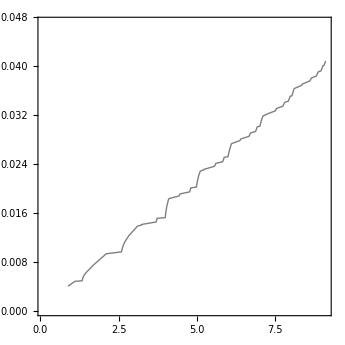

```mathematica
ListContourPlot[data,Contours->{1},ContourShading->None]
```